## Week4-10.x

Jacobi iteration method.

```mathematica
NestWhile[{x+1,y+1,z-1},]
```

```mathematica
ClearAll[x,y,z]
```

```mathematica
Table[
Nest[N@{{i,(7+#[[2]]-#[[3]])/4},{i,(21+4#[[1]]+#[[3]])/8},{i,(15+2#[[1]]-#[[2]])/5}}&,{1,1,1},i],
{i,1,50}]
```

{{{1.,1.75},{1.,3.25},{1.,3.2}},«48»,{{50.,{1.75,{6.96875,{3.8,{1.99062,{2.18633,{2.0675,{1.99965,{2.00699,{2.00253,{1.99999,{2.00026,{2.00009,{2.,{2.00001,{2.,{2.,{2.,{2.,«1»}}}}}}}}}}}}}}}}}}},«1»,{50.,{13.,{-3.075,{4.7625,«1»}}}}}}

```mathematica
datalist=Prepend[Table[
Nest[N@{(7+#[[2]]-#[[3]])/4,(21+4#[[1]]+#[[3]])/8,(15+2#[[1]]-#[[2]])/5}&,{1,1,1},i],
{i,1,10}],{1,1,1}]
```

{{1,1,1},{1.75,3.25,3.2},{1.7625,3.9,3.05},{1.9625,3.8875,2.925},{1.99062,3.97188,3.0075},{1.99109,3.99625,3.00188},{1.99859,3.99578,2.99719},{1.99965,3.99895,3.00028},{1.99967,3.99986,3.00007},{1.99995,3.99984,2.99989},{1.99999,3.99996,3.00001}}

Reshape the table

```mathematica
pltList=Join[{Table[datalist[[i,1]],{i,1,Length@datalist}]},{Table[datalist[[i,2]],{i,1,Length@datalist}]},{Table[datalist[[i,3]],{i,1,Length@datalist}]}]
```

{{1,1.75,1.7625,1.9625,1.99062,1.99109,1.99859,1.99965,1.99967,1.99995,1.99999},{1,3.25,3.9,3.8875,3.97188,3.99625,3.99578,3.99895,3.99986,3.99984,3.99996},{1,3.2,3.05,2.925,3.0075,3.00188,2.99719,3.00028,3.00007,2.99989,3.00001}}

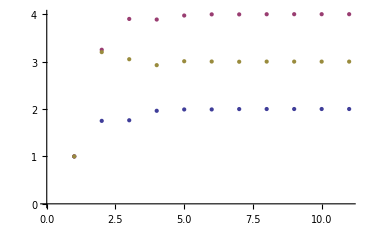

```mathematica
ListPlot[pltList]
```